```mathematica
tasks = {
    Sin[2*x^3]^2/x^3
    , (x^2 - 4)*Sin[(Pi*(x^2))/6] / (x^2 - 1)
    , Sqrt[Abs[3*x^3 + 2*x^2 - 10*x]] / (4*x)
    , 1/2 * Log[Sqrt[x^2 + 1] / Sqrt[x^2 - 1]] - 15*x^2
    , (x^3 - x^2 - x + 1)^(1/3) / Tan[x]
    , 2*Log[(x - 1) / x] + 1
    , Log[x - 1] / (x - 1)^2
};
```

```mathematica
getVariantForNumber[number_, variationsQuo_]:=(
    Module[{t},
        t = Mod[number , variationsQuo];
        If[t ≠ 0
                , t
                , variationsQuo
            ]
    ]
)
```

```mathematica
Table[Plot[tasks[[i]], {x, -10, 10}], {i, 1, Length[tasks]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
yourNumber = 17;
numberOfYourTask = getVariantForNumber[yourNumber, Length[tasks]];
Print["Number of your task: ", numberOfYourTask]
```

Number of your task: 3

```mathematica
f[y_] = tasks[[numberOfYourTask]] /. x->y
```

(√Abs[-10 y+2 y^2+3 y^3])/(4 y)

# Исследование функции

```mathematica
Plot[(√Abs[-10 x+2 x^2+3 x^3])/(4 x),{x,-8,8}]
```

-Graphics-

## Область определения и график функции

```mathematica
FunctionDomain[f[x],x]
```

x<0||x>0

```mathematica
ResourceFunction["FunctionParity"][f[x],x]
```

Undefined

```mathematica
FunctionPeriod[f[x],x]
```

0

Функция не является периодичной (FunctionPeriod вернула 0) , и не является четной, нечетной (FunctionParity вернула Undefined)

## Точки пересечения графика с осями координат

```mathematica
sols = Solve[f[x]==0, x]
points = {x, 0}/.sols 
g1 = Plot[f[x], {x, -10, 10}, PlotStyle->Blue];
g2 = ListPlot[points, PlotStyle->{Red, PointSize[Large]}];
Show[{g1, g2}]
```

{{x→1/3 (-1-√31)},{x→1/3 (-1+√31)}}

{{1/3 (-1-√31),0},{1/3 (-1+√31),0}}

-Graphics-

## Промежутки знакопостоянства

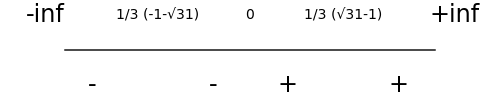

```mathematica
g1 = Graphics[Line[{{0,0}, {20,0}}]];

g2 = Graphics[Text[Style[-inf, 24], {-1, 1}]];
g3 = Graphics[Text[Style[1/3 (-1-√31), 14], {5, 1}]];
g4 = Graphics[Text[Style[0, 14], {10, 1}]];
g5 =  Graphics[Text[Style[1/3 (-1+√31), 14], {15, 1}]];
g6 = Graphics[Text[Style["+inf", 24], {21, 1}]];

g7 = Graphics[Text[Style["-", 24], {1.5, -1}]];
g8 = Graphics[Text[Style["-", 24], {8, -1}]];
g9 = Graphics[Text[Style["+", 24], {12, -1}]];
g10 = Graphics[Text[Style["+", 24], {18, -1}]];


Show[{g1, g2, g3, g4, g5, g6, g7, g8, g9, g10}, ImageSize->{500, 100}]
```

## Промежутки возрастания и убывания

```mathematica
ResourceFunction["FunctionMonotonicity"][Sqrt[3*x^3 + 2*x^2 - 10*x] / (4*x),x]
```

<|Increasing→1/3 (-1+√31)≤x,Decreasing→1/3 (-1-√31)≤x≤0,Constant→False|>

```mathematica
ResourceFunction["FunctionMonotonicity"][Sqrt[-(3*x^3 + 2*x^2 - 10*x)] / (4*x),x]
```

<|Increasing→x≤1/3 (-1-√31),Decreasing→0≤x≤1/3 (-1+√31),Constant→False|>

Так как производная модуля сложна для вольфрама, раскроем сами его. Получили 4 промежутка. склеиваем их.

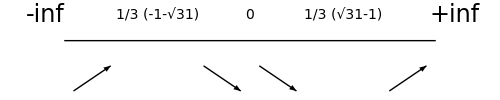

```mathematica
g1 = Graphics[Line[{{0,0}, {20,0}}]];

g2 = Graphics[Text[Style[-inf, 24], {-1, 1}]];
g3 = Graphics[Text[Style[1/3 (-1-√31), 14], {5, 1}]];
g4 = Graphics[Text[Style[0, 14], {10, 1}]];
g5 =  Graphics[Text[Style[1/3 (-1+√31), 14], {15, 1}]];
g6 = Graphics[Text[Style["+inf", 24], {21, 1}]];

g7 = Graphics[Arrow[{{0.5,-2}, {2.5,-1}}]];
g8 = Graphics[Arrow[{{7.5,-1}, {9.5,-2}}]];
g9 = Graphics[Arrow[{{10.5,-1}, {12.5,-2}}]];
g10 = Graphics[Arrow[{{17.5,-2}, {19.5,-1}}]];
Show[{g1, g2, g3, g4, g5, g6, g7, g8, g9, g10}, ImageSize->{500, 100}]
```

## Точки экстремума

По найденным промежуткам :
 -в 0 функции не существует;
 -две других являются точками локального максимума и минимума соответственно (слева на право).

## Точки разрыва

Точка разрыва в 0 для ее классификации посчитаем правый и левый предел.

```mathematica
Limit[f[x], x -> 0, Direction -> "FromAbove"]
Limit[f[x], x -> 0, Direction -> "FromBelow"]
```

∞

-∞

Эта    точка   разрыва второго    рода.

## Асимптоты

Начнем с вертикальных асимптот, в точке x = 0 оба предела бесконечны, значит x=0 вертикальная асимптота. Далее проверяем наклонные асимптоты:

```mathematica
k =Limit[f[x]/x, x -> Infinity]
Limit[ f[x]-k*x, x -> Infinity ]
```

0

∞

Так как предел не конечен, то наклонные асимптоты отсутствуют.

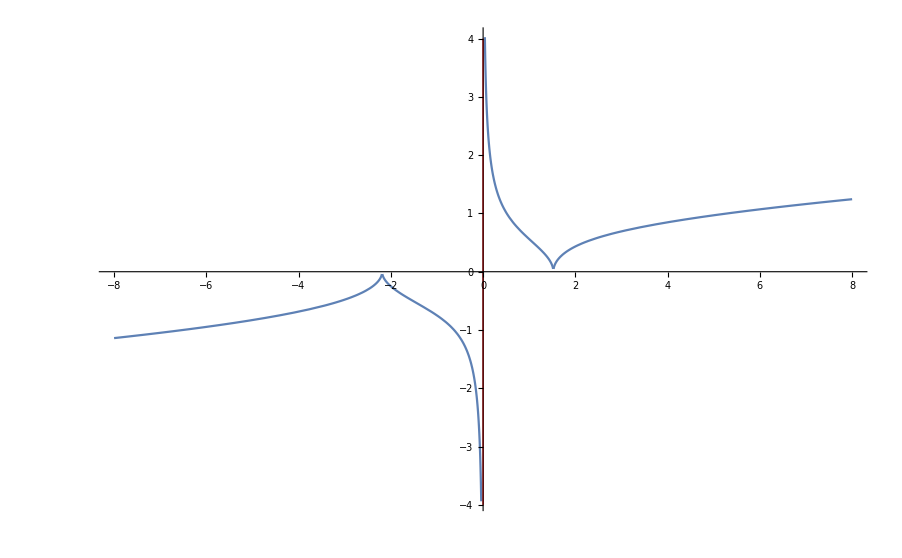

```mathematica
assimp = Graphics[ {Red,Line[{{0,-4}, {0,4}}]} ];
g = Plot[f[x],{x, -8, 8}];
Show[{g,assimp}]
```

```mathematica
ResourceFunction["FunctionOverview"][f[x],x,Dataset]
```

```mathematica
Plot[f'[x], {x, -8, 8}]
```

-Graphics-